```mathematica
m[ϕ_,θ_]:={Cos[ϕ]Cos[θ],Sin[ϕ]Cos[θ],Sin[θ]};
α1[α0_,αx_,αy_] := (λ*α0)/(√3) +  λ(αy/(√6)-αx/(√2));
α2[α0_,αx_,αy_] :=  (λ*α0)/(√3)+ λ(- (√2)/(√3)αy + (0*αx));
α3[α0_,αx_,αy_] := (λ*α0)/(√3) +   λ(αy/(√6)+αx/(√2));
β1[β0_,βx_,βy_] :=  λ(β0/(√3) + βy/(√6)-βx/(√2));
β2 [β0_,βx_,βy_] :=λ(β0/(√3) - (√2)/(√3)βy+ (0*βx));
β3[β0_,βx_,βy_] :=  λ(β0/(√3) + βy/(√6)+βx/(√2));
```

```mathematica
(*nearest neigbour*)
m3 = m[α3[a0 -(a/2)(a0dx/2+a0dy/(2 √3)),0,0]-π/6,β3[0,bx -(a/2)(bxdx/2+bxdy/(2 √3)),by-(a/2)(bydx/2+bydy/(2 √3))]];(*Gradient expansion with triangle center as the origin*)
m1 = m[α1[a0 + (a/2)(a0dx/2-a0dy/(2 √3)),0,0]-(5π)/6,β1[0,bx + (a/2)(bxdx/2-bxdy/(2 √3)),by + (a/2)(bydx/2-bydy/(2 √3))]];
m2 = m[α2[a0 +(a/2) (a0dy/(√3)),0,0]+π/2,β2[0,bx+(a/2)(bxdy/(√3)),by+(a/2)(bydy/(√3))]];
HeisJ = J/2(m1+m2+m3).(m1+m2+m3);
FullSimplify[Series[HeisJ,{λ,0,2},{dz,0,0}]]
```

1/32 a^2 (a0dx^2+a0dy^2+2 (bxdx+bydy)^2) J λ^2+O[λ]^3

```mathematica
(*next nearest neighbour*)
m3NN1 = m[α3[a0 +((3a0dx)/2-a0dy/(2 √3)),0,0]-π/6,β3[0,bx +((3bxdx)/2-bxdy/(2 √3)),by+((3bydx)/2-bydy/(2 √3))]];(*(3/2,-1/(2 √3))*)
m3NN2 = m[α3[a0 -((5a0dx)/2+a0dy/(2 √3)),0,0]-π/6,β3[0,bx -((5bxdx)/2+bxdy/(2 √3)),by-((5bydx)/2+bydy/(2 √3))]];(*(-5/2,-1/(2 √3))*)
m3NN3 = m[α3[a0 +(a0dx/2+(5a0dy)/(2 √3)),0,0]-π/6,β3[0,bx +(bxdx/2+(5bxdy)/(2 √3)),by+(bydx/2+(5bydy)/(2 √3))]];(*(1/2,5/(2 √3))*)
m3NN4 = m[α3[a0 -((3a0dx)/2+(7a0dy)/(2 √3)),0,0]-π/6,β3[0,bx -((3bxdx)/2+(7bxdy)/(2 √3)),by-((3bydx)/2+(7bydy)/(2 √3))]];(*(-3/2,-7/(2 √3))*)
m3 = m[α3[a0 -(a0dx/2+a0dy/(2 √3)),0,0]-π/6,β3[0,bx -(bxdx/2+bxdy/(2 √3)),by-(bydx/2+bydy/(2 √3))]];(*{-1/2,-1/(2 √3)}*)


m1NN1 = m[α1[a0 + (-a0dx/2+(5a0dy)/(2 √3)),0,0]-(5π)/6,β1[0,bx + (-bxdx/2+(5bxdy)/(2 √3)),by + (-bydx/2+(5bydy)/(2 √3))]];(*(-1/2,5/(2 √3))*)
m1NN2 = m[α1[a0 + ((3a0dx)/2-(7a0dy)/(2 √3)),0,0]-(5π)/6,β1[0,bx + ((3bxdx)/2-(7bxdy)/(2 √3)),by + ((3bydx)/2-(7bydy)/(2 √3))]];(*{3/2,-7/(2 √3)}*)
m1NN3 = m[α1[a0 - ((3a0dx)/2+a0dy/(2 √3)),0,0]-(5π)/6,β1[0,bx - ((3bxdx)/2+bxdy/(2 √3)),by - ((3bydx)/2+bydy/(2 √3))]];(*(-3/2,-1/(2 √3))*)
m1NN4 = m[α1[a0 + ((5a0dx)/2-a0dy/(2 √3)),0,0]-(5π)/6,β1[0,bx + ((5bxdx)/2-bxdy/(2 √3)),by + ((5bydx)/2-bydy/(2 √3))]];(*{5/2,-1/(2 √3)}*)
m1 = m[α1[a0 + (a0dx/2-a0dy/(2 √3)),0,0]-(5π)/6,β1[0,bx + (bxdx/2-bxdy/(2 √3)),by + (bydx/2-bydy/(2 √3))]];(*(+1/2,-1/(2 √3))*)


m2NN1 = m[α2[a0 - (a0dx+(2a0dy)/(√3)),0,0]+π/2,β2[0,bx-(bxdx+(2bxdy)/(√3)),by-(bydx+(2bydy)/(√3))]];(*{-1,-2/(√3)}*)
m2NN2 = m[α2[a0 - (3/2 a0dx+(7a0dy)/(2 √3)),0,0]+π/2,β2[0,bx-(3/2 bxdx+(7bxdy)/(2 √3)),by-(3/2 bydx+(7bydy)/(2 √3))]];(*{-3/2,-7/(2 √3)}*)
m2NN3 = m[α2[a0 - (-a0dx+(2a0dy)/(√3)),0,0]+π/2,β2[0,bx-(-bxdx+(2bxdy)/(√3)),by-(-bydx+(2bydy)/(√3))]];(*{1,-2/(√3)}*)
m2NN4 = m[α2[a0 - (a0dx-(4a0dy)/(√3)),0,0]+π/2,β2[0,bx-(bxdx-(4bxdy)/(√3)),by-(bydx-(4bydy)/(√3))]];(*{-1,4/(√3)}*)
m2 = m[α2[a0 + (a0dy/(√3)),0,0]+π/2,β2[0,bx+(bxdy/(√3)),by+(bydy/(√3))]];(*{0,1/(√3)}*)


HNN =-J2 (m1.(m1NN1 + m1NN2+m1NN3 + m1NN4) + m2.(m2NN1 + m2NN2+ m2NN3+ m2NN4) + m3.(m3NN1 + m3NN2+ m3NN3+ m3NN4))/2;

FullSimplify[Series[HNN,{λ,0,2}]]
```

-6 J2+1/48 (101 a0dx^2+10 √3 a0dx a0dy+111 a0dy^2+120 bxdx^2+72 bxdy^2+48 bxdy bydx+82 bydx^2+48 bxdx bydy+20 √3 bydx bydy+150 bydy^2) J2 λ^2+O[λ]^3

```mathematica
Expand[1/48 (+120 bxdx^2+72 bxdy^2+48 bxdy bydx+82 bydx^2+48 bxdx bydy+20 √3 bydx bydy+150 bydy^2)]
```

(5 bxdx^2)/2+(3 bxdy^2)/2+bxdy bydx+(41 bydx^2)/24+bxdx bydy+(5 bydx bydy)/(4 √3)+(25 bydy^2)/8

```mathematica
dispα =(J/4+101/24 JN) qx^2 + (J/4+111/48 JN)qy^2  + (10 √3)/24 JN qx qy;
dispβ = {{J/2 qx^2+JN(5 qx^2 + 3 qy^2),(J/2+JN(2+5/(4 √3)))qx qy},{(J/2+JN(2+5/(4 √3)))qx qy,J/2 qy^2+JN(41/12 qx^2+25/4 qy^2)}};
eigβ = Eigenvalues[dispβ];
JN = 0;
Simplify[eigβ[[1]]]
Simplify[eigβ[[2]]]
Clear[JN]
```

1/4 (J (qx^2+qy^2)-√(J^2 (qx^2+qy^2)^2))

1/4 (J (qx^2+qy^2)+√(J^2 (qx^2+qy^2)^2))

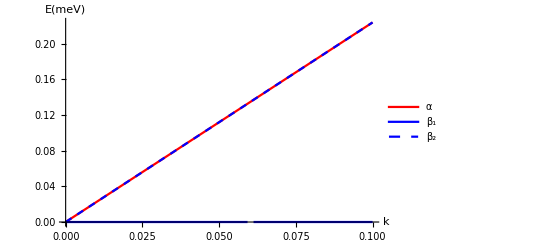

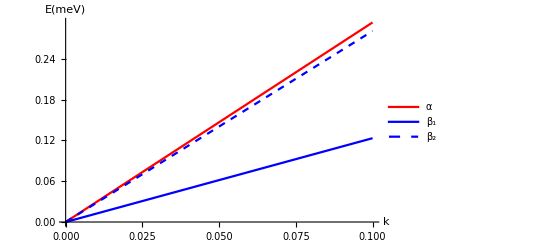

```mathematica
J = 10;
JN = 0;
qx = k;
qy = k;
tb = .1;
p1 = Plot[Sqrt[dispα],{k,0,tb},PlotRange->All,AxesOrigin->{0,0},PlotStyle->{Red,Thickness-> .013,Diamond},AxesStyle->Directive[Black,20],AxesLabel->{" k","E(meV)"},LabelStyle->Directive[Black],PlotLegends->{α}];
p2 = Plot[Sqrt[eigβ[[1]]/2],{k,0,tb},PlotRange->All,AxesOrigin->{0,0},PlotStyle->{Blue,Thickness-> .013},AxesStyle->Directive[Black,20],AxesLabel->{" k","E(meV)"},LabelStyle->Directive[Black],PlotLegends->{Subscript[β, 1]}];
p3 = Plot[Sqrt[eigβ[[2]]/2],{k,0,tb},PlotRange->All,AxesOrigin->{0,0},PlotStyle->{Blue,Dashed,Thickness-> .013},AxesStyle->Directive[Black,20],AxesLabel->{" k","E(meV)"},LabelStyle->Directive[Black],PlotLegends->{Subscript[β, 2]}];
JN = 0.5;
p4 = Plot[Sqrt[dispα],{k,0,tb},PlotRange->All,AxesOrigin->{0,0},PlotStyle->{Red,Thickness-> .013,Diamond},AxesStyle->Directive[Black,20],AxesLabel->{" k","E(meV)"},LabelStyle->Directive[Black],PlotLegends->{α}];
p5 = Plot[Sqrt[eigβ[[1]]/2],{k,0,tb},PlotRange->All,AxesOrigin->{0,0},PlotStyle->{Blue,Thickness-> .013},AxesStyle->Directive[Black,20],AxesLabel->{" k","E(meV)"},LabelStyle->Directive[Black],PlotLegends->{Subscript[β, 1]}];
p6 = Plot[Sqrt[eigβ[[2]]/2],{k,0,tb},PlotRange->All,AxesOrigin->{0,0},PlotStyle->{Blue,Dashed,Thickness-> .013},AxesStyle->Directive[Black,20],AxesLabel->{" k","E(meV)"},LabelStyle->Directive[Black],PlotLegends->{Subscript[β, 2]}];
Clear[J]
Clear[JN]
Clear[qx]
Clear[qy]
Show[{p1,p2,p3}]
Show[{p4,p5,p6}]
```

```mathematica
(*HEXAGONAL*)


m2 = m[α2[a0 ,0,0]+π/2,β2[0,bx,by]];

m11 = m[α1[a0 + (a0dx/2-(√3 a0dy)/2),0,0]-(5π)/6,β1[0,bx + (bxdx/2-(√3 bxdy)/2),by + (bydx/2-(√3 bydy)/2)]];
m12 = m[α1[a0 + (a0dx/2+(√3 a0dy)/2),0,0]-(5π)/6,β1[0,bx + (bxdx/2+(√3 bxdy)/2),by + (bydx/2+(√3 bydy)/2)]];
m13 = m[α1[a0 - (a0dx),0,0]-(5π)/6,β1[0,bx - (bxdx),by - (bydx)]];

m31 = m[α3[a0 - (a0dx/2+(√3 a0dy)/2),0,0]-π/6,β3[0,bx -(bxdx/2+(√3 bxdy)/2),by-(bydx/2+(√3 bydy)/2)]];
m32 = m[α3[a0 +(a0dx),0,0]-π/6,β3[0,bx +(bxdx),by+(bydx)]];
m33 = m[α3[a0 -(a0dx/2-(√3 a0dy)/2),0,0]-π/6,β3[0,bx -(bxdx/2-(√3 bxdy)/2),by-(bydx/2-(√3 bydy)/2)]];

(*m2 = m[α2[a0 ,a0,ax]+π/2,β2[b0,bx,by]];

m11 = m[α1[a0 ,a0,ax]-(5π)/6,β1[b0,bx,by]];
m12 = m[α1[a0 ,a0,ax]-(5π)/6,β1[b0,bx,by]];
m13 = m[α1[a0 ,a0,ax]-(5π)/6,β1[b0,bx,by]];

m31 = m[α3[a0 ,a0,ax]-π/6,β3[b0,bx,by]];
m32 = m[α3[a0 ,a0,ax]-π/6,β3[b0,bx,by]];
m33 = m[α3[a0 ,a0,ax]-π/6,β3[b0,bx,by]];*)




Heis1 =J/2(2m2.(m31 + m11+m32 + m12+m33+m13)+m31.m11 + m11.m32 + m32.m12 + m12.m33 + m33.m13 + m13.m31);
FullSimplify[Series[Heis1,{λ,0,2}]]
```

-(9 J)/2+3/8 (a0dx^2+a0dy^2+bxdx^2+bxdy^2+bydx^2+bydy^2) J λ^2+O[λ]^3

```mathematica
m2 = m[α2[a0 ,ax,ay]+π/2,β2[b0,bx,by]];

m11 = m[α1[a0 ,ax,ay]-(5π)/6,β1[b0,bx ,by ]];
m12 = m[α1[a0 ,ax,ay]-(5π)/6,β1[b0,bx ,by ]];
m13 = m[α1[a0 ,ax,ay]-(5π)/6,β1[b0,bx ,by ]];

m31 = m[α3[a0 ,ax,ay]-π/6,β3[b0,bx ,by ]];
m32 = m[α3[a0 ,ax,ay]-π/6,β3[b0,bx ,by ]];
m33 = m[α3[a0 ,ax,ay]-π/6,β3[b0,bx ,by ]];

Heis1 = J(m2.(m31 + m11+m32 + m12+m33+m13)+1/2(m31.m11 + m11.m32 + m32.m12 + m12.m33 + m33.m13 + m13.m31));
Kin = (α1[a0,ax,ay] β1[b0,bx,by]) +(α2[a0,ax,ay]  β2[b0,bx,by]) +(α3[a0,ax,ay]  β3[b0,bx,by]);
FullSimplify[Kin]
FullSimplify[Series[Heis1,{λ,0,2}]]
```

(a0 b0+ax bx+ay by) λ^2

-(9 J)/2+9/4 (ax^2+ay^2+2 b0^2) J λ^2+O[λ]^3

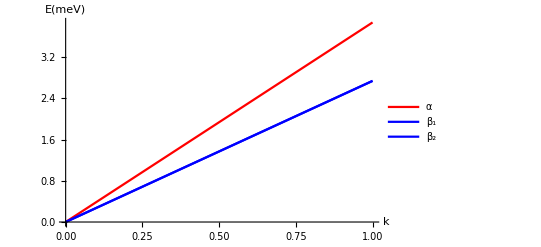

```mathematica
dispa = (3 J)/4(qx^2+qy^2);
dispb1 = (3 J)/4(qx^2+qy^2);
dispb2 = (3 J)/4(qx^2+qy^2);
J = 10;
qx = k;
qy = k;
tb = 1;
p1 = Plot[Sqrt[dispa],{k,0,tb},PlotRange->All,AxesOrigin->{0,0},PlotStyle->{Red,Thickness-> .013},AxesLabel->{"k","E(meV)"},AxesStyle->Directive[Black,20],LabelStyle->Directive[Black],PlotLegends->{α}];
p2 = Plot[Sqrt[dispb1/2],{k,0,tb},PlotRange->All,AxesOrigin->{0,0},PlotStyle->{Blue,Thickness-> .01},AxesStyle->Directive[Black,20],AxesLabel->{"k","E(meV)"},LabelStyle->Directive[Black],PlotLegends->{Subscript[β, 1]}];
p3 = Plot[Sqrt[dispb2/2],{k,0,tb},PlotRange->All,AxesOrigin->{0,0},PlotStyle->{Blue,Thickness-> .01},AxesStyle->Directive[Black,20],AxesLabel->{"k","E(meV)"},LabelStyle->Directive[Black],PlotLegends->{Subscript[β, 2]}];
Clear[J]
Clear[qx]
Clear[qy]
Show[{p1,p2,p3}]
```